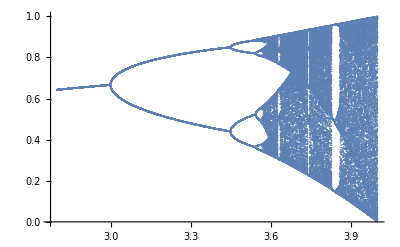

```mathematica
(* 1st - The function is better in pure function format: miu # (1-#) & *)
(* 2nd - Declare recursive shell with function above, x0 = 0.01, and iteration steps = 1000 as:
NestList[miu # (1-#) &,0.01,1000]
And it would be generate 1001 results in total including the initial one. *)
(* 3rd - Say only the last 100 results is desiered. Using "Part" (i.e.[[...]]) and "Span" (i.e. ;;) to perform the selection. The overall command would be like: NestList[miu # (1-#) &,0.01,1000][[-100 ;;]] *) 
(* 4th - Keeping track of the value of miu that generated each of those 100x values of the recursion, making transform each element in the list into a sublist of the form {miu,generatedvalue}, by mapping another simple pure function {miu,#}& on the list obtained from NestList (see "Map" and its shorthand "/@"):
{miu,#} & /@ NestList[miu # (1-#) &,0.01,1000][[-100 ;;]] *)
(* 5th - now need to apply this recursion to each value of miu in your interval of interest. We can use "Subdivide" to generate such a list: Subdivide[2.8,4,1200] *)
(* 6th - The step above will generate a list of 1201 values,i.e.1200 equally spaced subdivisions as requested. Then, using "Table" to run the recursion multiple times, each time with a different value of miu from that list above, and save the result in a variable called nestedlist:
nestedlist=Table[
{miu,#} & /@ NestList[miu # (1-#) &,0.01,1000][[-100 ;;]],{miu,Subdivide[2.8,4,1200]}]; *)
nestedlist=Table[
{miu,#} & /@ NestList[miu # (1-#) &,0.01,1000][[-100 ;;]],{miu,Subdivide[2.8,4,1200]}];
(* 7th - Using "Dimensions" to show that the "nestedlist" contains 1201 lists, one pervalue of miu, each of which contains 100 pairs of values, i.e.the {r,generatedvalue} pairs:
Dimensions[nestedlist]
(*Out:{1201,100,2}*) *)
(* 8th - However, the result above is too nested, it really only want a long list of such pairs, it can be flatten out the top level of this nested list, to obtain a list of 1201×100=120100 pairs. We use "Flatten" (together with a level specification, 1) for that,and save the result in a flatlist:
flatlist=Flatten[nestedlist,1];
(*Out:{120100,2}*) *)
flatlist=Flatten[nestedlist,1];
(* 9th - Finally, The bifuraction map is ready to be plot using "ListPlot":
ListPlot[flatlist] *)
ListPlot[flatlist]
```